```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Thu 1 Feb 2018 15:16:27

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.1.0 (December 27, 2017)

## At Day 10

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

## 4 Applications of Antiderivatives

## Lab 28: Arc Length and Surfaces of Revolution

### Estimating Arc Length

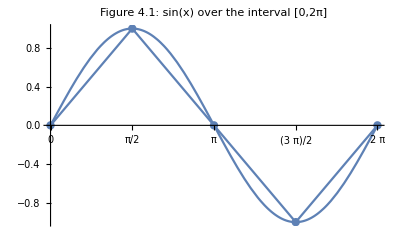

```mathematica
Show[Plot[Sin[x],{x,0,2π},Ticks->{{0,π/2,π,3 π/2,2π},Automatic},PlotLabel->"Figure 4.1: sin(x) over the interval [0,2π]"],ListLinePlot[Table[{x,Sin[x]},{x,0,2π,π/2}],Mesh->All]]
```

Exercise I:

a. Using 4 line segments,

```mathematica
L==∑_(i=0)^(n-1) √(Δx^2+(Sin[Subscript[x, i+1]]-Sin[Subscript[x, i]])^2)
SCMAF[%,RA,{At[2],Subscript[x, i_]->Subscript[x, 0]+Δx i},
RR,{At[2],{n==4,Subscript[x, 0]==0,Δx==(2π)/n}},
SCEvalSum,At[2],Apply->N]
```

L==∑_(i=0)^(-1+n) √(Δx^2+(-Sin[x_i]+Sin[x_(1+i)])^2)

L==∑_(i=0)^3 √(π^2/4+(-Sin[(i π)/2]+Sin[1/2 (1+i) π])^2)

L==7.44838

b. Using 8 line segments,

```mathematica
L==∑_(i=0)^(n-1) √(Δx^2+(Sin[Subscript[x, i+1]]-Sin[Subscript[x, i]])^2)
SCMAF[%,RA,{At[2],Subscript[x, i_]->Subscript[x, 0]+Δx i},
RR,{At[2],{n==8,Subscript[x, 0]==0,Δx==(2π)/n}},
SCEvalSum,At[2],Apply->N]
```

L==∑_(i=0)^(-1+n) √(Δx^2+(-Sin[x_i]+Sin[x_(1+i)])^2)

L==∑_(i=0)^7 √(π^2/16+(-Sin[(i π)/4]+Sin[1/4 (1+i) π])^2)

L==7.58018

Using infinitely many line segments,

```mathematica
L==Underscript[Limit, n->∞][∑_(i=0)^(n-1) √(Δx^2+(f[Subscript[x, i+1]]-f[Subscript[x, i]])^2)]
SCMAF[%,RA,{At[2],Subscript[x, i_]->Subscript[x, 0]+Δx i},
SCFactor,{Δx^2+(-f[i Δx+Subscript[x, 0]]+f[(1+i) Δx+Subscript[x, 0]])^2,Δx^2},ApplyAll->PowerExpand]
```

L==Limit_(n→∞)[∑_(i=0)^(-1+n) √(Δx^2+(-f[x_i]+f[x_(1+i)])^2)]

L==Limit_(n→∞)[∑_(i=0)^(-1+n) √(Δx^2+(-f[i Δx+x_0]+f[(1+i) Δx+x_0])^2)]

L==Limit_(n→∞)[∑_(i=0)^(-1+n) Δx √(1+(-f[i Δx+x_0]+f[(1+i) Δx+x_0])^2/Δx^2)]

Exercises I:

c.

```mathematica
L==∫_a^b √(f'[x]^2+1)ⅆx
SCMAF[%,RA,{At[2],{a==0,b==2π,f->Function[{x},Sin[x]]}},
SCEvalInt,At[2],Apply->N]
```

L==∫_a^b √(1+f'[x]^2)ⅆx

L==∫_0^(2 π) √(1+Cos[x]^2)ⅆx

L==7.6404

e.

The accuracy for n=4,

```mathematica
7.44838/7.6404 100
```

97.4868

The accuracy for n=8,

```mathematica
7.58018/7.6404 100
```

99.2118

### Surfaces of Revolution

```mathematica
Show[RevolutionPlot3D[√(x^2-1),{x,1,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotRange->All,PlotStyle->Opacity[0.8]],
RevolutionPlot3D[√(x^2-1),{x,1.55,1.6},RevolutionAxis->{1, 0, 0}]]
```

-Graphics3D-

Exercise II:

a. If the height of the cylinder is denoted h, what is the surface area of one cylinder wall with radius y=f(x)?

```mathematica
ⅆS==2π y h;
```

b.

```mathematica
S==∫_a^b 2π y hⅆx
SCMAF[%,RA,{At[2],{y==f[x],h==√(1+(ⅆf[x]/ⅆx)^2)}}]
```

S==∫_a^b 2 h π yⅆx

S==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx

Exercise III:

a.

```mathematica
g[x]==√(16-4 x^2)
SCMAF[%,RevolutionPlot3D,{At[2],{x,0,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},Boxed->False,AxesLabel->{x,y,z},PlotRange->All},Part->2]
```

g[x]==√(16-4 x^2)

-Graphics3D-

```mathematica
h[x]==Log[x]
SCMAF[%,RevolutionPlot3D,{At[2],{x,1.5,4},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},Boxed->False,AxesLabel->{x,y,z},PlotStyle->Opacity[0.8],PlotRange->All},Part->2]
```

h[x]==Log[x]

-Graphics3D-

```mathematica
Show[RevolutionPlot3D[√(16-4 x^2),{x,0,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotRange->All,PlotStyle->Opacity[0.7]],
RevolutionPlot3D[Log[x],{x,1.5,4},RevolutionAxis->{1,0,0},PlotStyle->Opacity[0.9]]]
```

-Graphics3D-

b.

```mathematica
Subscript[S, g]==2 π ∫_a^b g[x] √(1+(ⅆg[x]/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{a==0,b==2,g[x]==√(16-4 x^2)}},Apply->SCEvalDeriv,
SCEvalInt,At[2],Apply->N]
```

S_g==2 π ∫_a^b g[x] √(1+(ⅆg[x]/ⅆx)^2)ⅆx

S_g==2 π ∫_0^2 √(16-4 x^2) √(1+(16 x^2)/(16-4 x^2))ⅆx

S_g==69.3751

```mathematica
Subscript[S, h]==2 π ∫_a^b h[x] √(1+(ⅆh[x]/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{a==1.5,b==4,h[x]==Log[x]}},Apply->SCEvalDeriv,
SCEvalInt,At[2]]
```

S_h==2 π ∫_a^b h[x] √(1+(ⅆh[x]/ⅆx)^2)ⅆx

S_h==2 π ∫_1.5^4 Log[x] √(1+1/x^2)ⅆx

S_h==16.3364

c.

```mathematica
RevolutionPlot3D[Sin[x],{x,π/4,(7π)/4},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotStyle->Opacity[0.8],PlotRange->All]
```

-Graphics3D-

The surface integral vanishes.

```mathematica
Subscript[S, f]==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{a==π/4,b==(7π)/4,f[x]==Sin[x]}},Apply->SCEvalDeriv,
SCEvalInt,At[2]]
```

S_f==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx

S_f==2 π ∫_(π/4)^((7 π)/4) √(1+Cos[x]^2) Sin[x]ⅆx

S_f==0

The integral results are antisymmetry with respect to the x=π plane.

```mathematica
{Subscript[S, f]==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx,Subscript[S, f]==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx}
SCMAF[%,RA,{{At[1],{a==π/4,b==π,f[x]==Sin[x]}},{At[2],{a==π,b==(7π)/4,f[x]==Sin[x]}}},Apply->SCEvalDeriv,
SCEvalInt,All,Apply->N]
```

{S_f==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx,S_f==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx}

{S_f==2 π ∫_(π/4)^π √(1+Cos[x]^2) Sin[x]ⅆx,S_f==2 π ∫_π^((7 π)/4) √(1+Cos[x]^2) Sin[x]ⅆx}

{S_f==12.0012,S_f==-12.0012}

```mathematica
Subscript[S, f]==2 2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{a==π/4,b==π,f[x]==Sin[x]}},Apply->SCEvalDeriv,
SCEvalInt,At[2],Apply->N]
```

S_f==4 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx

S_f==4 π ∫_(π/4)^π √(1+Cos[x]^2) Sin[x]ⅆx

S_f==24.0023

d.

```mathematica
RevolutionPlot3D[{x,√(16-4 x^2),0},{x,0,2},RevolutionAxis->{0,1,0},AxesOrigin->{0,0,0},BoxRatios->1, AxesLabel->{x,y,z},Boxed->False,PlotStyle->Opacity[0.8],PlotRange->All]
```

-Graphics3D-

y==√(16-4 x^2)

x==(√(16-y^2))/2

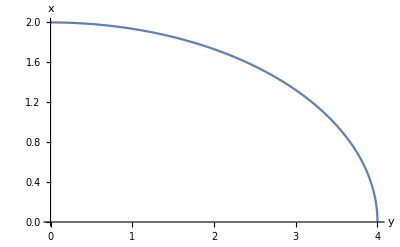

```mathematica
y==√(16-4 x^2)
SCMAF[%,SCSolve,{All,x},Part->2,
Plot,{At[2],{y,0,4},AxesLabel->{y,x}},Part->2]
```

```mathematica
Subscript[S, g^-1]==2 π ∫_a^b (g^-1)[y] √(1+((ⅆ(g^-1)[y])/ⅆy)^2)ⅆy
SCMAF[%,RA,{At[2],{a==0,b==4,(g^-1)[y]==(√(16-y^2))/2}},Apply->SCEvalDeriv,
SCEvalInt,At[2],Apply->N]
```

S_(g^-1)==2 π ∫_a^b g^-1[y] √(1+((ⅆg^-1[y])/ⅆy)^2)ⅆy

S_(g^-1)==π ∫_0^4 √(16-y^2) √(1+y^2/(4 (16-y^2)))ⅆy

S_(g^-1)==42.9569

## Lab 29: Volumes

### The Disk Method

Exercises I:

a.

```mathematica
RevolutionPlot3D[√(x^2-1),{x,1,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},PlotStyle->Opacity[0.8],Boxed->False,PlotRange->All]
```

-Graphics3D-

b.

```mathematica
V==Underscript[limit, n->∞][∑_(i=0)^(n-1) π f[Subscript[x, i]]^2 Δx];
```

```mathematica
V==∫_a^b π f[x]^2 ⅆx
SCMAF[%,RA,{At[2],{a==1,b==2,f[x]==√(x^2-1)}},Apply->SCEvalInt]
```

V==∫_a^b π f[x]^2ⅆx

V==(4 π)/3

c.

```mathematica
Show[RevolutionPlot3D[√(x^2-1),{x,1,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotRange->All],RevolutionPlot3D[x-1,{x,1,2},RevolutionAxis->{1,0,0}]]
```

-Graphics3D-

```mathematica
V==Subscript[V, 1]-Subscript[V, 2]
SCMAF[%,RA,{At[2],{Subscript[V, 1]==∫_a^b π (Subscript[f, 1][x])^2 ⅆx,Subscript[V, 2]==∫_a^b π (Subscript[f, 2][x])^2 ⅆx}},
RA,{At[2],{a==1,b==2,Subscript[f, 1][x]==√(x^2-1),Subscript[f, 2][x]==x-1}},Apply->SCEvalInt]
```

V==V_1-V_2

V==π ∫_a^b f_1[x]^2 ⅆx-π ∫_a^b f_2[x]^2 ⅆx

V==π

### The Cylindrical Shell Method

```mathematica
RevolutionPlot3D[{x,x^2-x^3,0},{x,0,1},RevolutionAxis->{0,1,0},AxesOrigin->{0,0,0},BoxRatios->1,PlotStyle->Opacity[0.8],AxesLabel->{x,y,z},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
V==∫_a^b 2π x f[x]ⅆx;
SCMAF[%,RA,{At[2],{a==0,b==1,f[x]==2π x(x^2-x^3)}},
SCEvalInt,At[2],$,Apply->N]
```

V==4 π^2 ∫_0^1 x^2 (x^2-x^3)ⅆx

V==(2 π^2)/15

Example II:

a, b.

```mathematica
Show[RevolutionPlot3D[{x,4x-x^2,0},{x,0,3},RevolutionAxis->{0,1,0},AxesOrigin->{0,0,0},PlotStyle->Opacity[0.8],AxesLabel->{x,y,z},Boxed->False,PlotRange->All],RevolutionPlot3D[{x,x,0},{x,0,3},RevolutionAxis->{0,1,0},PlotStyle->Opacity[0.8]]]
```

-Graphics3D-

c.

```mathematica
V==∫_a^b 2π x f[x]ⅆx;
```

```mathematica
V==Subscript[V, 1]-Subscript[V, 2]
SCMAF[%,RA,{At[2],{Subscript[V, 1]==∫_a^b 2π x Subscript[f, 1][x]ⅆx,Subscript[V, 2]==∫_a^b 2π x Subscript[f, 2][x]ⅆx}},
RA,{At[2],{a==0,b==3,Subscript[f, 1][x]==4x-x^2,Subscript[f, 2][x]==x}},
SCEvalInt,At[2],$,Apply->N]
```

V==V_1-V_2

V==-2 π ∫_0^3 x^2 ⅆx+2 π ∫_0^3 x (4 x-x^2)ⅆx

V==(27 π)/2

d. Rotate about the line x=-1.

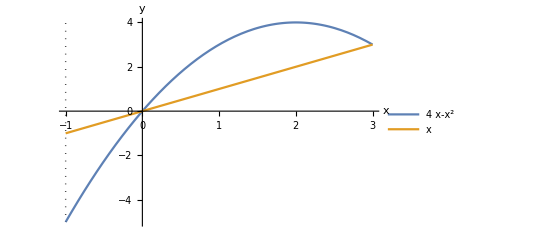

```mathematica
Plot[{4x-x^2,x},{x,-1,3},AxesLabel->{x,y},PlotLegends->"Expressions",Epilog->{Dotted,Line[{{-1,5},{-1,-5}}]}(*,AspectRatio->Automatic*)]
```

```mathematica
Translate[#,{-1,0,0}]&@@Show[
RevolutionPlot3D[{x+1,4x-x^2,0},{x,-1,3},RevolutionAxis->{0,1,0},PlotStyle->Opacity[0.8]],
RevolutionPlot3D[{x+1,x,0},{x,-1,3},RevolutionAxis->{0,1,0},PlotStyle->Opacity[0.8]]];
%//Graphics3D[#,Boxed->False,Axes->True,AxesLabel->{x,y,z},AxesOrigin->{0,0,0},PlotRange->All]&
```

-Graphics3D-

e.

```mathematica
S==Subscript[S, 1]+Subscript[S, 2]
SCMAF[%,RA,{At[2],{Subscript[S, 1]==∫_-1^0 2π (1+x)(x-(4x-x^2))ⅆx,Subscript[S, 2]==∫_0^3 2π (x+1)((4x-x^2)-x)ⅆx}},Apply->SCEvalInt]
```

S==S_1+S_2

S==(71 π)/3

f.

```mathematica
y==4x-x^2
SCMAF[%,SCSolve,{All,x}]
```

y==4 x-x^2

{{x==2-√(4-y)},{x==2+√(4-y)}}

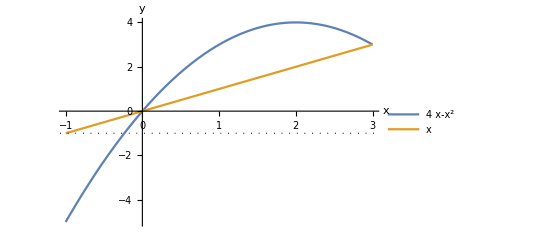

```mathematica
Plot[{4x-x^2,x},{x,-1,3},AxesLabel->{x,y},PlotLegends->"Expressions",Epilog->{Dotted,Line[{{-5,-1},{5,-1}}]}(*,AspectRatio->Automatic*)]
```

```mathematica
Solve[4x-x^2==-1,x]
```

{{x→2-√5},{x→2+√5}}

```mathematica
Translate[#,{0,-1,0}]&@@Show[RevolutionPlot3D[{x,4x-x^2+1,0},{x,0,3},RevolutionAxis->{1,0,0},PlotStyle->Opacity[0.8]],
RevolutionPlot3D[{x,x+1,0},{x,0,3},RevolutionAxis->{1,0,0},PlotStyle->Opacity[0.8]]];
%//Graphics3D[#,Boxed->False,Axes->True,AxesLabel->{x,y,z},AxesOrigin->{0,0,0},PlotRange->All]&
```

-Graphics3D-

```mathematica
V==∫_0^3 π f[x]^2 ⅆx-∫_0^3 π g[x]^2 ⅆx
SCMAF[%,RA,{At[2],{f[x]==4x-x^2+1,g[x]==x+1}},Apply->SCEvalInt]
```

V==∫_0^3 π f[x]^2ⅆx-∫_0^3 π g[x]^2ⅆx

V==(153 π)/5

g.

## Lab 30: Work

### Introduction

Demonstration: Work of Raising a Leaky Bucket

Exercises: There are 10 kg of water in a bucket, the bucket is pulled up, by the rope, at a constant velocity 1m/s from the ground and leaks out 1 kg  of water per second. t represents time and 0≤t≤10.

a. Determine the work to lift the empty bucket.

```mathematica
Subscript[W, b]==Subscript[M, b] g L
SCMAF[%,RA,{At[2],{Subscript[M, b]==Quantity[5, "Kilograms"],g==Quantity[9.8, ("Meters")/("Seconds")^2],L==Quantity[10, "Meters"]}},
UnitConvert,{At[2],"Joules"}]
```

W_b==g L M_b

W_b==490. kg m^2/s^2

W_b==490. J

b. Determine the work to lift the empty bucket, for t seconds.

```mathematica
Subscript[W, b]==∫_0^l Subscript[M, b] gⅆx
SCMAF[%,SCTransInt,{At[2],TransVar->{x,t,x==v t}},Apply->SCEvalInt,
RA,{At[2],l==v t}]
```

W_b==∫_0^l g M_bⅆx

W_b==g l M_b

W_b==g t v M_b

c. Determine the work to lift the rope for t seconds.

```mathematica
Subscript[W, r]==∫_0^t Subscript[m, r] g  vⅆ t'
SCMAF[%,RR,{At[2],{Subscript[m, r]==ρ l,ρ==Subscript[M, r]/L,l==L-v t'}},Apply->SCEvalInt]
```

W_r==∫_0^t g v m_rⅆ t'

W_r==g t v M_r-(g t^2 v^2 M_r)/(2 L)

d. Determine the amount of water in the bucket after t seconds.

```mathematica
Subscript[m, w]==Subscript[M, w]-Subscript[Δm, w] t;
```

e. Determine the work to lift the water for t seconds.

```mathematica
Subscript[W, w]==∫_0^t Subscript[m, w] g vⅆ t'
SCMAF[%,RA,{At[2],Subscript[m, w]==Subscript[M, w]-Subscript[Δm, w] t'},Apply->SCEvalInt]
```

W_w==∫_0^t g v m_wⅆ t'

W_w==g t v M_w-1/2 g t^2 v Δm_w

f. Determine the entire work to lift the bucket/water/rope.

```mathematica
W==Subscript[W, b]+Subscript[W, r]+Subscript[W, w]
SCMAF[%,RA,{At[2],{Subscript[W, b]==g t v Subscript[M, b],Subscript[W, r]==g t v Subscript[M, r]-(g t^2 v^2 Subscript[M, r])/(2 L),Subscript[W, w]==g t v Subscript[M, w]-1/2 g t^2 v Subscript[Δm, w]}},
RA,{At[2],t==T},
RA,{At[2],{Subscript[M, b]==Quantity[5, "Kilograms"],Subscript[M, r]==Quantity[0.8, "Kilograms"],Subscript[M, w]==Quantity[10, "Kilograms"],g==Quantity[9.8, ("Meters")/("Seconds")^2],L==Quantity[10, "Meters"],v==Quantity[1, ("Meters")/("Seconds")],T==Quantity[10, "Seconds"],Subscript[Δm, w]==Quantity[1, ("Kilograms")/("Seconds")]}},
UnitConvert,{At[2],"Joules"}]
```

W==W_b+W_r+W_w

W==1019.2 kg m^2/s^2

W==1019.2 J

## Lab 31: Differential Equations

### Separable Differential Equations

Exercises I:

```mathematica
{ⅆx/ⅆt==Cos[2t],ⅆy/ⅆt==Cos[3t]};
```

a. Determine the value of t in the interval [-π,π] for which x and y increase simultaneously.

{ⅆx/ⅆt==Cos[2 t],ⅆy/ⅆt==Cos[3 t]}

{ⅆx/ⅆt,ⅆy/ⅆt}=={Cos[2 t],Cos[3 t]}

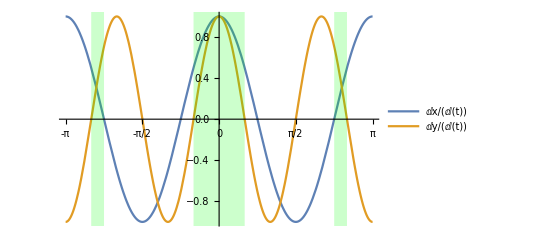

```mathematica
{ⅆx/ⅆt==Cos[2t],ⅆy/ⅆt==Cos[3t]}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{t,-π,π},PlotLegends->At[1],Ticks->{Table[-π+i π/4,{i,0,8}],Automatic},
Epilog->{Green,Opacity[0.2],Rectangle[{-(5π)/6,-2},{-(3π)/4,2}],Rectangle[{(3π)/4,-2},{(5π)/6,2}],Rectangle[{-π/6,-2},{π/6,2}]
}},Part->2]
```

```mathematica
ⅆx/ⅆt==Cos[2t]
SCMAF[%,RA,{At[1],ⅆx/ⅆt==0},
Reduce,{All,t},Apply->ExpandAll]
```

ⅆx/ⅆt==Cos[2 t]

0==Cos[2 t]

C[1]∈ℤ&&(t==-π/4+π C[1]||t==π/4+π C[1])

```mathematica
ⅆy/ⅆt==Cos[3 t]
SCMAF[%,RA,{At[1],ⅆy/ⅆt==0},
Reduce,{All,t},Apply->ExpandAll]
```

ⅆy/ⅆt==Cos[3 t]

0==Cos[3 t]

C[1]∈ℤ&&(t==-π/6+2/3 π C[1]||t==π/6+2/3 π C[1])

```mathematica
{-π/6-2/3 π<t<-3/4 π ,-π/6<t<π/6,3/4 π<t<π/6+2/3 π};
```

b. Determine the value of t in the interval [-π,π] for which x increases while and y decreases simultaneously.

{ⅆx/ⅆt==Cos[2 t],ⅆy/ⅆt==Cos[3 t]}

{ⅆx/ⅆt,ⅆy/ⅆt}=={Cos[2 t],Cos[3 t]}

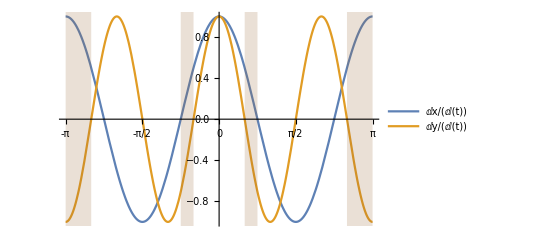

```mathematica
{ⅆx/ⅆt==Cos[2t],ⅆy/ⅆt==Cos[3t]}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{t,-π,π},PlotLegends->At[1],Ticks->{Table[-π+i π/4,{i,0,8}],Automatic},
Epilog->{Brown,Opacity[0.2],Rectangle[{-π,-2},{-(5π)/6,2}],Rectangle[{(5π)/6,-2},{π,2}],Rectangle[{-π/4,-2},{-π/6,2}],Rectangle[{π/6,-2},{π/4,2}]}},Part->2]
```

```mathematica
ⅆx/ⅆt==Cos[2t]
SCMAF[%,RA,{At[1],ⅆx/ⅆt==0},
Reduce,{All,t},Apply->ExpandAll]
```

ⅆx/ⅆt==Cos[2 t]

0==Cos[2 t]

C[1]∈ℤ&&(t==-π/4+π C[1]||t==π/4+π C[1])

```mathematica
ⅆy/ⅆt==Cos[3 t]
SCMAF[%,RA,{At[1],ⅆy/ⅆt==0},
Reduce,{All,t},Apply->ExpandAll]
```

ⅆy/ⅆt==Cos[3 t]

0==Cos[3 t]

C[1]∈ℤ&&(t==-π/6+2/3 π C[1]||t==π/6+2/3 π C[1])

```mathematica
{- π<t<-(5π)/6,-π/4<t<-π/6,π/6<t<π/4,(5π)/6<t<π};
```

c.

```mathematica
{ⅆx/ⅆt==Cos[2t],ⅆy/ⅆt==Cos[3t]}
SCMAF[%,SCDerivToFrac,{At[All,1]},
SCMultEq,{All,ⅆt},Level->{1},Apply->SCDiffToInt,
SCEvalInt,All]
```

{ⅆx/ⅆt==Cos[2 t],ⅆy/ⅆt==Cos[3 t]}

{∫1ⅆx==∫Cos[2 t]ⅆt,∫1ⅆy==∫Cos[3 t]ⅆt}

{x==1/2 Sin[2 t],y==1/3 Sin[3 t]}

d.

{x==1/2 Sin[2 t],y==1/3 Sin[3 t]}

{x,y}=={1/2 Sin[2 t],1/3 Sin[3 t]}

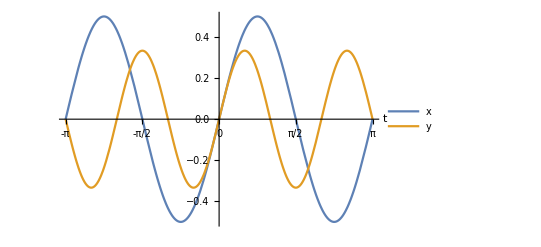

```mathematica
{x==1/2 Sin[2 t],y==1/3 Sin[3 t]}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{t,-π,π},AxesLabel->Automatic,Ticks->{Table[-π+i π/4,{i,0,8}],Automatic},PlotLegends->At[1]},Part->2]
```

### An Epidemic Model

Exercises II:

The following model represents the growth of epidemic
ⅆA/ⅆt=c A(P-A)
where A is the number of people affected by the virus at time t, P is a constant representing the total population, and c is a constant.

a. Determine A(t) using separation of variables.

```mathematica
ⅆA/ⅆt==c A(P-A)
SCMAF[%,SCDerivToFrac,At[1],
SCMultEq,{All,ⅆt/(A(P-A))},Apply->SCDiffToInt,
SCEvalInt,{All,ReplConst->d},
SCSolve,{All,A},
RA,{All,{A->A[t],C[2]->0}},
SCDivFrac,{All,ⅇ^(d P+c P t)},
Factor,{-d P-c P t+P C[2]}]
```

ⅆA/ⅆt==A c (-A+P)

A[t]==P/(1-ⅇ^(-d P-c P t))

A[t]==P/(1-ⅇ^(-d P-c P t))

```mathematica
{A[t]==P/(1-ⅇ^(-d P-c P t))/.t->0,A[t]==P/(1-ⅇ^(-d P-c P t))/.t->10}
SCMAF[%,RA,{All,{A[0]==100,A[10]==1000,P==50000}},
SCSolve,{All,{c,d}},RA->{C[_]->0}]
```

{A[0]==P/(1-ⅇ^(-d P)),A[10]==P/(1-ⅇ^(-10 c P-d P))}

{100==50000/(1-ⅇ^(-50000 d)),1000==50000/(1-ⅇ^(-500000 c-50000 d))}

{c==1/500000 Log[499/49],d==(-ⅈ π-Log[499])/50000}

```mathematica
A[t]==P/(1-ⅇ^(-d P-c P t))
SCMAF[%,RA,{At[2],{c==1/500000 Log[499/49],d==(-ⅈ π-Log[499])/50000,P==50000}},Apply->ComplexExpand]
```

A[t]==P/(1-ⅇ^(-d P-c P t))

A[t]==50000/(1+7^(t/5) 499^(1-t/10))

A[t]==50000/(1+7^(t/5) 499^(1-t/10))

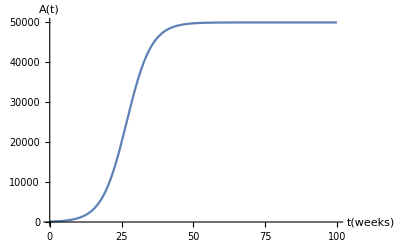

```mathematica
A[t]==50000/(1+7^(t/5) 499^(1-t/10))
SCMAF[%,Plot,{At[2],{t,0,100},AxesLabel->{t["weeks"],A[t]}},Part->2]
```

b, c. Check the answer with result from DSolve.

```mathematica
ⅆA/ⅆt==c A(P-A)
SCMAF[%,RA,{All,A->A[t]},
SCDSolve,{All,A[0]==100,A[t],t},
SCDivFrac,{At[2],100 ⅇ^(c P t)},
Factor,{-ⅇ^(-c P t)+1/100 ⅇ^(-c P t) P},IgnoreError->True]
```

ⅆA/ⅆt==A c (-A+P)

A[t]==P/(1-ⅇ^(-c P t)+1/100 ⅇ^(-c P t) P)

A[t]==P/(1+1/100 ⅇ^(-c P t) (-100+P))

```mathematica
A[t]==P/(1+1/100 ⅇ^(-c P t) (-100+P))
SCMAF[%,RR,{All,{t==10,A[10]==1000,P==50000}},
SCSolve,{All,c},RA->{C[1]->0}]
```

A[t]==P/(1+1/100 ⅇ^(-c P t) (-100+P))

1000==50000/(1+499 ⅇ^(-500000 c))

c==1/500000 Log[499/49]

```mathematica
A[t]==P/(1+1/100 ⅇ^(-c P t) (-100+P))
SCMAF[%,RA,{At[2],{c==1/500000 Log[499/49],P==50000}}]
```

A[t]==P/(1+1/100 ⅇ^(-c P t) (-100+P))

A[t]==50000/(1+7^(t/5) 499^(1-t/10))

d. When does the epidemic spread the fastest?

```mathematica
SCARA[(ⅆ^2 A[t])/(ⅆ t^2),A[t]==50000/(1+7^(t/5) 499^(1-t/10)),Apply->SCEvalDeriv]
SCMAF[%,RA,{At[1],(ⅆ^2 A[t])/(ⅆ t^2)==0},ApplyAll->Simplify,
SCSolve,{All,t},Apply->N]
```

(ⅆ^2 A[t])/(ⅆ t^2)==50000 (2/((1+7^(t/5) 499^(1-t/10))^3) (1/5 7^(t/5) 499^(1-t/10) Log[7]-1/10 7^(t/5) 499^(1-t/10) Log[499])^2-1/((1+7^(t/5) 499^(1-t/10))^2) (1/25 7^(t/5) 499^(1-t/10) Log[7]^2-1/25 7^(t/5) 499^(1-t/10) Log[7] Log[499]+1/100 7^(t/5) 499^(1-t/10) Log[499]^2))

(7^(2 t/5) 499^(1+t/10)-3493^(t/5))/(499 7^(t/5)+499^(t/10))==0

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

SCMAF::stopped: Stopped due to error.

t==26.7694

## Lab 32: Improper Integrals

### Infinite Intervals

Exercises:

a, b, c.

```mathematica
SCAFE[{∫_1^2 1/x^2 ⅆx,∫_1^10 1/x^2 ⅆx,∫_1^100 1/x^2 ⅆx},SCEvalInt]
SCMAF[%,Thread,All,Apply->N]
```

{∫_1^2 1/x^2 ⅆx,∫_1^10 1/x^2 ⅆx,∫_1^100 1/x^2 ⅆx}=={1/2,9/10,99/100}

{∫_1.^2. 1/x^2 ⅆx==0.5,∫_1.^10. 1/x^2 ⅆx==0.9,∫_1.^100. 1/x^2 ⅆx==0.99}

d.

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/x^2 ⅆx],SCEvalInt,{All,Assumptions->n>1}]
SCMAF[%,SCEvalLimit,At[2]]
```

Limit_(n→∞)[∫_1^n 1/x^2 ⅆx]==Limit_(n→∞)[(-1+n)/n]

Limit_(n→∞)[∫_1^n 1/x^2 ⅆx]==1

Integration over an infinite interval or over a discontinuity, is called an improper integral.

e.

```mathematica
SCAFE[{∫_1^10 1/x^3 ⅆx,∫_1^10 1/x^4 ⅆx,∫_1^10 1/x^5 ⅆx},SCEvalInt]
SCMAF[%,Thread,All,Apply->N]
```

{∫_1^10 1/x^3 ⅆx,∫_1^10 1/x^4 ⅆx,∫_1^10 1/x^5 ⅆx}=={99/200,333/1000,9999/40000}

{∫_1.^10. 1/x^3 ⅆx==0.495,∫_1.^10. 1/x^4 ⅆx==0.333,∫_1.^10. 1/x^5 ⅆx==0.249975}

f.

```mathematica
SCAFE[{∫_1^100 1/x^3 ⅆx,∫_1^100 1/x^4 ⅆx,∫_1^100 1/x^5 ⅆx},SCEvalInt]
SCMAF[%,Thread,All,Apply->N]
```

{∫_1^100 1/x^3 ⅆx,∫_1^100 1/x^4 ⅆx,∫_1^100 1/x^5 ⅆx}=={9999/20000,333333/1000000,99999999/400000000}

{∫_1.^100. 1/x^3 ⅆx==0.49995,∫_1.^100. 1/x^4 ⅆx==0.333333,∫_1.^100. 1/x^5 ⅆx==0.25}

g.

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/x^p ⅆx],SCEvalInt,{All,Assumptions->{p>1,n>1}}]
SCMAF[%,SCEvalLimit,At[2]]
```

```mathematica
Underscript[Limit, n->∞][∫_1^n x^-p ⅆx]==Underscript[Limit, n->∞][(n^-p (-n+n^p))/(-1+p)]
```

Limit_(n→∞)[∫_1^n x^-p ⅆx]==Limit_(n→∞)[(n^-p (-n+n^p))/(-1+p)]

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/x ⅆx],SCEvalInt,{All,Assumptions->{n>1}}]
SCMAF[%,SCEvalLimit,At[2]]
```

Limit_(n→∞)[∫_1^n 1/x ⅆx]==Limit_(n→∞)[Log[n]]

Limit_(n→∞)[∫_1^n 1/x ⅆx]==∞

h.

```mathematica
SCAFE[{∫_1^100 1/x ⅆx,∫_1^1000 1/x ⅆx},SCEvalInt]//Thread
```

{∫_1^100 1/x ⅆx==Log[100],∫_1^1000 1/x ⅆx==Log[1000]}

i.

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/x ⅆx],SCEvalInt,{All,Assumptions->{n>1}},Apply->SCEvalLimit]
```

Limit_(n→∞)[∫_1^n 1/x ⅆx]==∞

```mathematica
Integrate[1/x,{x,1,∞}]
```

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

∫_1^∞ 1/x ⅆx

Discontinuous Integrands

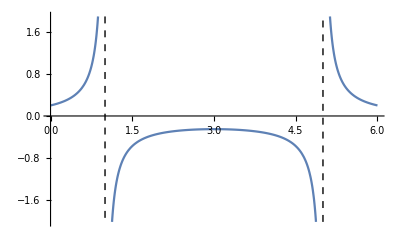

```mathematica
Plot[1/(x^2-6x+5),{x,0,6},ExclusionsStyle->Dashed]
```

```mathematica
∫_0^1 1/(x^2-6x+5)ⅆx==Underscript[Limit, a->1][∫_0^a 1/(x^2-6x+5)ⅆx]
SCMAF[%,SCEvalInt,{At[2]},
SCEvalLimit,{At[2],Direction->"FromBelow"}]
```

∫_0^1 1/(5-6 x+x^2)ⅆx==Limit_(a→1)[∫_0^a 1/(5-6 x+x^2)ⅆx]

∫_0^1 1/(5-6 x+x^2)ⅆx==Limit_(a→1)[ConditionalExpression[1/4 (-Log[5]-Log[1-a]+Log[5-a]),Re[a]≤1||a∉ℝ]]

∫_0^1 1/(5-6 x+x^2)ⅆx==∞

Exercises:

j, k.

```mathematica
SCAFE[{∫_(.0001)^1 1/x^(.5)ⅆx,∫_(.000001)^1 1/x^(.5)ⅆx},SCEvalInt]//Thread
```

{∫_0.0001^1 x^-0.5 ⅆx==1.98,∫_(1.×10^-6)^1 x^-0.5 ⅆx==1.998}

l.

```mathematica
SCAFE[{∫_(.0001)^1 1/x^(.25)ⅆx,∫_(.0001)^1 1/x^(.2)ⅆx},SCEvalInt]//Thread
```

{∫_0.0001^1 x^-0.25 ⅆx==1.332,∫_0.0001^1 x^-0.2 ⅆx==1.24921}

m.

```mathematica
SCAFE[{∫_(.000001)^1 1/x^(.25)ⅆx,∫_(.000001)^1 1/x^(.2)ⅆx},SCEvalInt]//Thread
```

{∫_(1.×10^-6)^1 x^-0.25 ⅆx==1.33329,∫_(1.×10^-6)^1 x^-0.2 ⅆx==1.24998}

n.

```mathematica
SCAFE[Underscript[Limit, n->0][∫_n^1 1/x^p ⅆx],SCEvalInt,{All,Assumptions->{0<n<1}}]
SCMAF[%,SCEvalLimit,{All,Direction->"FromAbove"},
Refine,{All,0<p<1}]
```

Limit_(n→0)[∫_n^1 x^-p ⅆx]==Limit_(n→0)[(n^-p (n-n^p))/(-1+p)]

ConditionalExpression[Limit_(n→0)[∫_n^1 x^-p ⅆx]==1/(1-p),0<p<1]

Limit_(n→0)[∫_n^1 x^-p ⅆx]==1/(1-p)

o.

```mathematica
SCAFE[{∫_(.0001)^1 1/x ⅆx,∫_(.000001)^1 1/x ⅆx},SCEvalInt]//Thread
```

{∫_0.0001^1 1/x ⅆx==9.21034,∫_(1.×10^-6)^1 1/x ⅆx==13.8155}

p.

```mathematica
SCAFE[Underscript[Limit, n->0][∫_n^1 1/x ⅆx],SCEvalInt,{All,Assumptions->{0<n<1}}]
SCMAF[%,SCEvalLimit,{At[2],Direction->"FromAbove"}]
```

Limit_(n→0)[∫_n^1 1/x ⅆx]==Limit_(n→0)[-Log[n]]

Limit_(n→0)[∫_n^1 1/x ⅆx]==∞

```mathematica
Integrate[1/x,{x,0,1}]
```

Integrate::idiv: Integral of 1/x does not converge on {0,1}.

∫_0^1 1/x ⅆx

## Lab 33: Comparison Test for Integrals

The Comparison Test

If b is a real number or ∞ and f(x)≥g(x)>0 on the interval [a,b) then
1. If ∫_a^b f(x)ⅆx converges then ∫_a^b g(x)ⅆx converges and
2. If ∫_a^b g(x)ⅆx diverges then ∫_a^b f(x)ⅆx diverges.

Exercise:

a.

{f[x]==ⅇ^-x,g[x]==ⅇ^(-x^2)}

{f[x],g[x]}=={ⅇ^-x,ⅇ^(-x^2)}

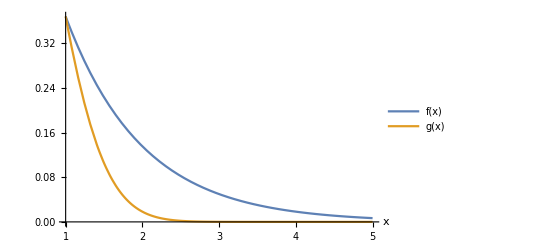

```mathematica
{f[x]==ⅇ^-x,g[x]==ⅇ^(-x^2)}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{x,1,5},AxesLabel->{x},PlotLegends->At[1]},Part->2]
```

b.

c.

```mathematica
SCAFE[∫_1^∞ ⅇ^-x ⅆx,SCEvalInt]
```

∫_1^∞ ⅇ^-x ⅆx==1/ⅇ

d.

By the comparison test, ∫_1^∞ ⅇ^-x ⅆx converges.

e.

```mathematica
SCAFE[∫_1^∞ ⅇ^(-x^2)ⅆx,SCEvalInt,Apply->N]
```

∫_1^∞ ⅇ^(-x^2)ⅆx==0.139403

f.

{f[x]==ⅇ^-x,g[x]==ⅇ^(-x^2),h[x]==1/x}

{f[x],g[x],h[x]}=={ⅇ^-x,ⅇ^(-x^2),1/x}

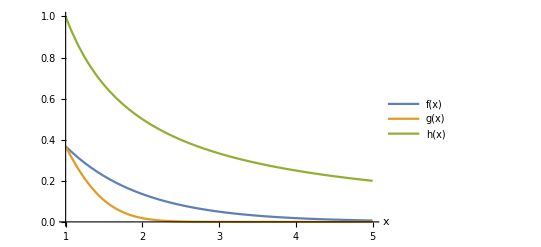

```mathematica
{f[x]==ⅇ^-x,g[x]==ⅇ^(-x^2),h[x]==1/x}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{x,1,5},AxesLabel->{x},PlotLegends->At[1]},Part->2]
```

∫_1^∞ h(x)ⅆx diverges, and h(x)>f(x)≥g(x). This does not correspond to any case of the comparison test.

g.

{1/x,1/(√x)}

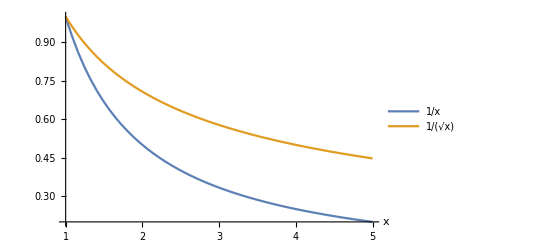

```mathematica
{1/x,1/(√x)}
SCMAF[%,Plot,{All,{x,1,5},AxesLabel->{x},PlotLegends->"Expressions"}]
```

1/(√x)≥1/x>0 on the interval [1,∞) and ∫_1^∞ 1/x ⅆx diverges. Therefore, ∫_1^∞ 1/(√x)ⅆx also diverges.

h.

```mathematica
Integrate[1/(√x),{x,1,∞}]
```

Integrate::idiv: Integral of 1/(√x) does not converge on {1,∞}.

∫_1^∞ 1/(√x)ⅆx

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/(√x)ⅆx],SCEvalInt,{All,Assumptions->{n>1}}]
SCMAF[%,SCEvalLimit,{At[2]}]
```

Limit_(n→∞)[∫_1^n 1/(√x)ⅆx]==Limit_(n→∞)[2 (-1+√n)]

Limit_(n→∞)[∫_1^n 1/(√x)ⅆx]==∞